```mathematica
<<ComputationalGeometry`
Needs["TetGenLink`"];
Clear[s];
BordaS[sigma_,sigmaP_] := (n=Length[sigma];Sum[(n-Position[sigma,i][[1]][[1]])*(n-Position[sigmaP,i][[1]][[1]]),{i,1,n}]);
Mat[S_,n_]:=(P=Permutations[Range[1,n],{n}];Table[Table[S[sigma,sigmaP],{sigmaP,P}],{sigma,P}]);
dot[A_,B_]:=(k=Length[A];Sum[A[[i]]*B[[i]],{i,1,n}]);
R[S_,n_]:=(M = Mat[S,n];Print[MatrixForm[M]];nf = Factorial[n];
T = Total[M[[1,All]]];
For[i=1,i≤nf,i++,
For[j=1,j≤nf,j++,
M[[i,j]]-=T/nf;
]
];
Print[Eigenvalues[M]];EV=Eigenvectors[M]; Print[MatrixForm[Transpose[EV]]];
k = MatrixRank[M];Print[k];
{M,k});
```

(5 | 4 | 4 | 2 | 2 | 1
4 | 5 | 2 | 1 | 4 | 2
4 | 2 | 5 | 4 | 1 | 2
2 | 1 | 4 | 5 | 2 | 4
2 | 4 | 1 | 2 | 5 | 4
1 | 2 | 2 | 4 | 4 | 5)

{6,6,0,0,0,0}

(-1 | 0 | 1 | 1 | 0 | -1
-1 | 1 | 0 | -1 | 1 | 1
0 | -1 | 0 | 0 | 0 | 1
1 | -1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0)

2

{{{2,1,1,-1,-1,-2},{1,2,-1,-2,1,-1},{1,-1,2,1,-2,-1},{-1,-2,1,2,-1,1},{-1,1,-2,-1,2,1},{-2,-1,-1,1,1,2}},2}

2

True

True

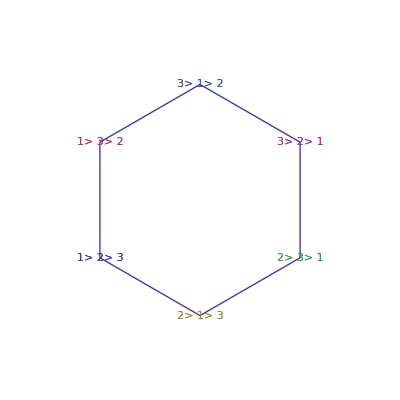

```mathematica
n = 3;
nf = Factorial[n];
P = Permutations[Range[1,n],{n}];
{M,k} = R[BordaS,n]
MM = Append[Mat[BordaS,n],ConstantArray[1,nf]];
Print[MatrixRank[MM]-1];
Print[M.Transpose[M]==Transpose[M].M];
{U,DD,V} = SingularValueDecomposition[M];
EMB = U.MatrixPower[DD,1/2][[All,Range[1,k]]];
Print[EMB.Transpose[EMB]==M];
LB = Table["\""<>StringReplace[ToString[P[[i]]],{"{"->"","}"->"",","->">"}]<>"\"",{i,1,nf}];
CV = EMB[[ConvexHull[EMB]]];
Show[ListPlot[Partition[EMB,1],PlotMarkers->LB,AspectRatio->1],ListLinePlot[Append[CV,CV[[1]]]],PlotRange->{{-2,2},{-2,2}},Ticks->None,Axes->None]
```

```mathematica
n = 4;
nf = Factorial[n];
P = Permutations[Range[1,n],{n}];
{M,k} = R[BordaS,n]
MM = Append[Mat[BordaS,n],ConstantArray[1,nf]];
Print[MatrixRank[MM]-1];
Print[M.Transpose[M]==Transpose[M].M];
{U,DD,V} = SingularValueDecomposition[M];
EMB = U.MatrixPower[DD,1/2][[All,Range[1,k]]];
Print[EMB.Transpose[EMB]==M];
LB = Table[StringReplace[ToString[P[[i]]],{"{"->"","}"->"",","->">"}],{i,1,nf}];
{pts,surface} = TetGenConvexHull[EMB];
Show[Append[Table[Graphics3D[Text[LB[[i]],EMB[[i]]]],{i,1,nf}],Graphics3D[{Opacity[1],GraphicsComplex[pts,Polygon[surface]]},AspectRatio->1]],Ticks->None,Axes->None,Boxed->False]
```

(14 | 13 | 13 | 11 | 11 | 10 | 13 | 12 | 11 | 8 | 9 | 7 | 11 | 9 | 10 | 7 | 6 | 5 | 8 | 7 | 7 | 5 | 5 | 4
13 | 14 | 11 | 10 | 13 | 11 | 12 | 13 | 9 | 7 | 11 | 8 | 8 | 7 | 7 | 5 | 5 | 4 | 11 | 9 | 10 | 7 | 6 | 5
13 | 11 | 14 | 13 | 10 | 11 | 11 | 9 | 10 | 7 | 6 | 5 | 13 | 12 | 11 | 8 | 9 | 7 | 7 | 8 | 5 | 4 | 7 | 5
11 | 10 | 13 | 14 | 11 | 13 | 8 | 7 | 7 | 5 | 5 | 4 | 12 | 13 | 9 | 7 | 11 | 8 | 9 | 11 | 6 | 5 | 10 | 7
11 | 13 | 10 | 11 | 14 | 13 | 9 | 11 | 6 | 5 | 10 | 7 | 7 | 8 | 5 | 4 | 7 | 5 | 13 | 12 | 11 | 8 | 9 | 7
10 | 11 | 11 | 13 | 13 | 14 | 7 | 8 | 5 | 4 | 7 | 5 | 9 | 11 | 6 | 5 | 10 | 7 | 12 | 13 | 9 | 7 | 11 | 8
13 | 12 | 11 | 8 | 9 | 7 | 14 | 13 | 13 | 11 | 11 | 10 | 10 | 7 | 11 | 9 | 5 | 6 | 7 | 5 | 8 | 7 | 4 | 5
12 | 13 | 9 | 7 | 11 | 8 | 13 | 14 | 11 | 10 | 13 | 11 | 7 | 5 | 8 | 7 | 4 | 5 | 10 | 7 | 11 | 9 | 5 | 6
11 | 9 | 10 | 7 | 6 | 5 | 13 | 11 | 14 | 13 | 10 | 11 | 11 | 8 | 13 | 12 | 7 | 9 | 5 | 4 | 7 | 8 | 5 | 7
8 | 7 | 7 | 5 | 5 | 4 | 11 | 10 | 13 | 14 | 11 | 13 | 9 | 7 | 12 | 13 | 8 | 11 | 6 | 5 | 9 | 11 | 7 | 10
9 | 11 | 6 | 5 | 10 | 7 | 11 | 13 | 10 | 11 | 14 | 13 | 5 | 4 | 7 | 8 | 5 | 7 | 11 | 8 | 13 | 12 | 7 | 9
7 | 8 | 5 | 4 | 7 | 5 | 10 | 11 | 11 | 13 | 13 | 14 | 6 | 5 | 9 | 11 | 7 | 10 | 9 | 7 | 12 | 13 | 8 | 11
11 | 8 | 13 | 12 | 7 | 9 | 10 | 7 | 11 | 9 | 5 | 6 | 14 | 13 | 13 | 11 | 11 | 10 | 5 | 7 | 4 | 5 | 8 | 7
9 | 7 | 12 | 13 | 8 | 11 | 7 | 5 | 8 | 7 | 4 | 5 | 13 | 14 | 11 | 10 | 13 | 11 | 7 | 10 | 5 | 6 | 11 | 9
10 | 7 | 11 | 9 | 5 | 6 | 11 | 8 | 13 | 12 | 7 | 9 | 13 | 11 | 14 | 13 | 10 | 11 | 4 | 5 | 5 | 7 | 7 | 8
7 | 5 | 8 | 7 | 4 | 5 | 9 | 7 | 12 | 13 | 8 | 11 | 11 | 10 | 13 | 14 | 11 | 13 | 5 | 6 | 7 | 10 | 9 | 11
6 | 5 | 9 | 11 | 7 | 10 | 5 | 4 | 7 | 8 | 5 | 7 | 11 | 13 | 10 | 11 | 14 | 13 | 8 | 11 | 7 | 9 | 13 | 12
5 | 4 | 7 | 8 | 5 | 7 | 6 | 5 | 9 | 11 | 7 | 10 | 10 | 11 | 11 | 13 | 13 | 14 | 7 | 9 | 8 | 11 | 12 | 13
8 | 11 | 7 | 9 | 13 | 12 | 7 | 10 | 5 | 6 | 11 | 9 | 5 | 7 | 4 | 5 | 8 | 7 | 14 | 13 | 13 | 11 | 11 | 10
7 | 9 | 8 | 11 | 12 | 13 | 5 | 7 | 4 | 5 | 8 | 7 | 7 | 10 | 5 | 6 | 11 | 9 | 13 | 14 | 11 | 10 | 13 | 11
7 | 10 | 5 | 6 | 11 | 9 | 8 | 11 | 7 | 9 | 13 | 12 | 4 | 5 | 5 | 7 | 7 | 8 | 13 | 11 | 14 | 13 | 10 | 11
5 | 7 | 4 | 5 | 8 | 7 | 7 | 9 | 8 | 11 | 12 | 13 | 5 | 6 | 7 | 10 | 9 | 11 | 11 | 10 | 13 | 14 | 11 | 13
5 | 6 | 7 | 10 | 9 | 11 | 4 | 5 | 5 | 7 | 7 | 8 | 8 | 11 | 7 | 9 | 13 | 12 | 11 | 13 | 10 | 11 | 14 | 13
4 | 5 | 5 | 7 | 7 | 8 | 5 | 6 | 7 | 10 | 9 | 11 | 7 | 9 | 8 | 11 | 12 | 13 | 10 | 11 | 11 | 13 | 13 | 14)

{40,40,40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

(-3 | 0 | 0 | 1 | 8 | 0 | 2 | 10 | 7 | 0 | 5 | -2 | -7 | 4 | -2 | -2 | -4 | -3 | -10 | -5 | -8 | 3 | 2 | 2
-8 | 1 | 4 | 0 | -3 | 0 | -3 | -6 | -6 | 1 | 0 | 2 | 6 | 0 | 3 | 1 | 0 | 2 | 6 | 0 | 3 | -2 | -2 | -1
0 | 0 | -3 | 0 | -4 | 1 | 2 | -5 | -2 | 0 | -4 | 1 | 2 | -5 | -2 | 2 | 5 | 2 | 5 | 4 | 4 | -2 | -1 | -2
-2 | 1 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-10 | 2 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
-7 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0
-5 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0
6 | -2 | -3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0
7 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-4 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6 | -1 | -6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 0 | -5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9 | -2 | -6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | -2 | -5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8 | -1 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-9 | 2 | 6 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-6 | 2 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-6 | 1 | 6 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

3

{{{5,4,4,2,2,1,4,3,2,-1,0,-2,2,0,1,-2,-3,-4,-1,-2,-2,-4,-4,-5},{4,5,2,1,4,2,3,4,0,-2,2,-1,-1,-2,-2,-4,-4,-5,2,0,1,-2,-3,-4},{4,2,5,4,1,2,2,0,1,-2,-3,-4,4,3,2,-1,0,-2,-2,-1,-4,-5,-2,-4},{2,1,4,5,2,4,-1,-2,-2,-4,-4,-5,3,4,0,-2,2,-1,0,2,-3,-4,1,-2},{2,4,1,2,5,4,0,2,-3,-4,1,-2,-2,-1,-4,-5,-2,-4,4,3,2,-1,0,-2},{1,2,2,4,4,5,-2,-1,-4,-5,-2,-4,0,2,-3,-4,1,-2,3,4,0,-2,2,-1},{4,3,2,-1,0,-2,5,4,4,2,2,1,1,-2,2,0,-4,-3,-2,-4,-1,-2,-5,-4},{3,4,0,-2,2,-1,4,5,2,1,4,2,-2,-4,-1,-2,-5,-4,1,-2,2,0,-4,-3},{2,0,1,-2,-3,-4,4,2,5,4,1,2,2,-1,4,3,-2,0,-4,-5,-2,-1,-4,-2},{-1,-2,-2,-4,-4,-5,2,1,4,5,2,4,0,-2,3,4,-1,2,-3,-4,0,2,-2,1},{0,2,-3,-4,1,-2,2,4,1,2,5,4,-4,-5,-2,-1,-4,-2,2,-1,4,3,-2,0},{-2,-1,-4,-5,-2,-4,1,2,2,4,4,5,-3,-4,0,2,-2,1,0,-2,3,4,-1,2},{2,-1,4,3,-2,0,1,-2,2,0,-4,-3,5,4,4,2,2,1,-4,-2,-5,-4,-1,-2},{0,-2,3,4,-1,2,-2,-4,-1,-2,-5,-4,4,5,2,1,4,2,-2,1,-4,-3,2,0},{1,-2,2,0,-4,-3,2,-1,4,3,-2,0,4,2,5,4,1,2,-5,-4,-4,-2,-2,-1},{-2,-4,-1,-2,-5,-4,0,-2,3,4,-1,2,2,1,4,5,2,4,-4,-3,-2,1,0,2},{-3,-4,0,2,-2,1,-4,-5,-2,-1,-4,-2,2,4,1,2,5,4,-1,2,-2,0,4,3},{-4,-5,-2,-1,-4,-2,-3,-4,0,2,-2,1,1,2,2,4,4,5,-2,0,-1,2,3,4},{-1,2,-2,0,4,3,-2,1,-4,-3,2,0,-4,-2,-5,-4,-1,-2,5,4,4,2,2,1},{-2,0,-1,2,3,4,-4,-2,-5,-4,-1,-2,-2,1,-4,-3,2,0,4,5,2,1,4,2},{-2,1,-4,-3,2,0,-1,2,-2,0,4,3,-5,-4,-4,-2,-2,-1,4,2,5,4,1,2},{-4,-2,-5,-4,-1,-2,-2,0,-1,2,3,4,-4,-3,-2,1,0,2,2,1,4,5,2,4},{-4,-3,-2,1,0,2,-5,-4,-4,-2,-2,-1,-1,2,-2,0,4,3,2,4,1,2,5,4},{-5,-4,-4,-2,-2,-1,-4,-3,-2,1,0,2,-2,0,-1,2,3,4,1,2,2,4,4,5}},3}

3

True

True

-Graphics3D-